## Ugeseddel 1: Simplex

## Opgave 1: plot og simplex

### (a) og (b)

```mathematica
z[x1_,x2_]:=2x1+x2
```

```mathematica
b1[x1_,x2_]:=x2
```

```mathematica
b2[x1_,x2_]:=2x1+5x2
```

```mathematica
b3[x1_,x2_]:=x1+x2
```

```mathematica
b4[x1_,x2_]:=3x1+x2
```

```mathematica
bv={10,60,18,44};
```

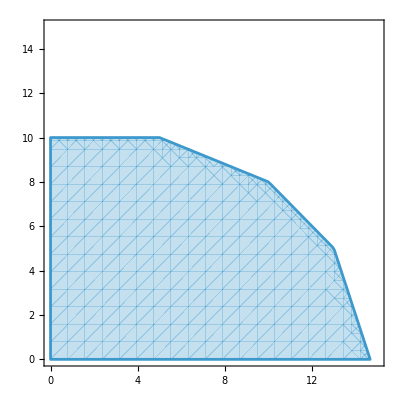

```mathematica
rp = RegionPlot[{
b1[x1,x2]<=bv[[1]]&&
b2[x1,x2]<=bv[[2]]&&
b3[x1,x2]<=bv[[3]]&&
b4[x1,x2]<=bv[[4]]
},{x1,0,15},{x2,0,15}]
```

```mathematica
ContourPlot[{
z[x1,x2]==zl,
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]],
b4[x1,x2]==bv[[4]]
},{x1,0,15},{x2,0,15}]
```

```mathematica
Manipulate[
Show[
rp,
ContourPlot[{
z[x1,x2]==zl,
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]],
b4[x1,x2]==bv[[4]]
},{x1,0,15},{x2,0,15}],PlotLegends->"Expressions"],
{zl,0,50}]
```

Show::gcomb: Could not combine the graphics objects in 
    Show[rp, -Graphics-, PlotLegends -> Expressions].

Den blå linje er objektfunktionen. Vi kan se at maximum er ved en værdi af objektfunktionen på 31. 
Her skærer bibetingelsen 3 x_1+x_2<=44 bibetingelsen x_1+x_2<=18 hinanden. Hvis vi vi løser ligningerne

3 x_1+x_2=44
x_1+x_2=18

```mathematica
Solve[{3x1+x2==44,x1+x2==18}]
```

{{x1→13,x2→5}}

Ser vi at optimum er når x_1=13 og x_2=5.

### (c)

Vi løser problemet med simplex-metoden.
Vi starter med at opstille tableauet

Derefter køres primal simplex

Det ses at vi får præcis samme løsning.

## Opgave 2: Simplex

### (a)

Her ses det ønskede tableau

Hvor der er indført en slackvariabel for hver bibetingelse.

### (b)

Vi løser problemet med simplex-metoden

Vi ser at den optimale løsning er når (x_1,x_2,x_3)=(0,10,6.67) og her bliver værdien af objektfunktionen Z=70.

## Opgave 3: plot og omskrivning af simplex (ikke løse)

### (a)

For at illustrere problemet, defineres de givne informationer

```mathematica
Clear["Global`*"]
```

```mathematica
z[x1_,x2_]:=5x1+7x2
```

```mathematica
b1[x1_,x2_]:=2x1+3x2
```

```mathematica
b2[x1_,x2_]:=3x1+4x2
```

```mathematica
b3[x1_,x2_]:=x1+x2
```

```mathematica
bv:={42,60,18}
```

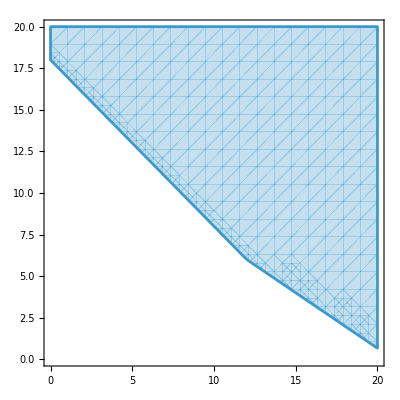

```mathematica
rp=RegionPlot[{
b1[x1,x2]>=bv[[1]]&&
b2[x1,x2]>=bv[[2]]&&
b3[x1,x2]>=bv[[3]]
},{x1,0,20},{x2,0,20}]
```

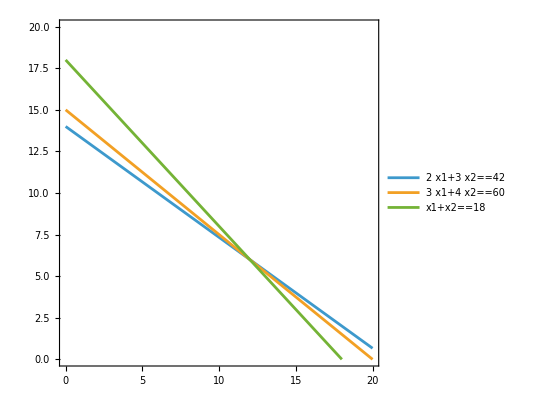

```mathematica
cp=ContourPlot[{
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]]
},{x1,0,20},{x2,0,20},PlotLegends->"Expressions"]
```

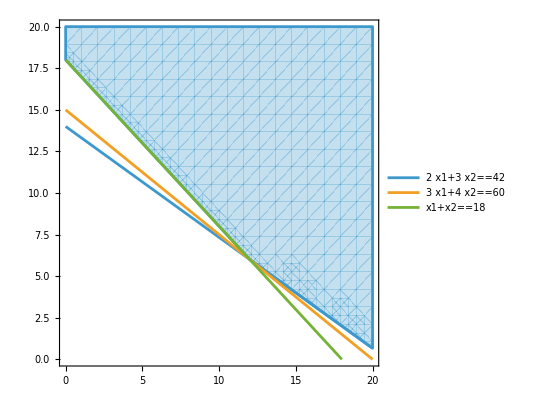

```mathematica
Show[rp,cp]
```

Ud fra vores skitse, kan vi se at bibetingelsen 3 x_1+4 x_2>=60 er overflødig. Den bidrager ikke med noget ny information, da den aldrig er aktiv alene. Denne kan vi altså med fordel smide væk, eftersom problemet ville være det samme, hvis denne ikke var der.

### (c)

Ved at gange objektivfunktionen med minus et, kan vi omdanne problemet fra et minimeringsproblem, til et maksimeringsproblem. Det samme kan vi gøre for bibetingelserne, så de passer i simplex algoritmen. Da bliver problemet

max -4 x_1-7 x_2
u.b.b
-2 x_1-3 x_2<=-42
-3 x_1-4 x_2<=-60
-x_1-x_2<=-18
x_1,x_2>=0

### (d)

Vi ser at objektiv koefficienterne alle er negative, hvormed de vil være positive, ligeså snart de kommer ind tableauet, og det vil ligne at vi befinder os i en optimal løsning med det samme. Derudover er (0,0) ikke inkluderet som en BFS, og dermed vil vi starte vores algoritme uden for mulighedsområdet, hvilket ikke vil virke for simplex algoritmen.

## Opgave 4: formulering af betingelser og simplex

### (a)

Vi definerer to beslutningsvariable, en for hver produkttype. 
x_1=mængde af produkttype 1
x_2=mængde af produkttype 2
Vi ved at profitten er givet ved 1 krone for produkt 1 og 2 kroner for produkt 2. Dermed bliver objektiv funktionen z=x_1+2 x_2 hvor z måler profit i kroner.

### (b) og (c)

Her ses en oversigt over rescourcebrug for de forskellige produkttyper, samt mængden er rescourcer til rådighed

Rescourceforbrug/Produkttype | x_1 | x_2 | Kapacitet
Rescource 1 | 1 | 3 | 200
Rescource 2 | 2 | 2 | 300

Derudover kan der maksimalt sælges 60 enheder af produkt 2. Da bliver bibetingelserne

x_1+3 x_2<=200
2 x_1+2 x_2<=300⟹x_1+x_2<=150
x_2<=60

### (d)

Vi får det samlede maksimeringsproblem

max x_1+2 x_2
u.b.b
x_1+3 x_2<=200
x_1+x_2<=150
x_2<=60
x_1,x_2>=0

Vi løser problemet med simplex.
Her ses tableauet

Vi løser med simplex

Her ses løsningstableuaet

Vi ser at den optimale værdi for objektivfunktionen er 175. Her produceres 125 enheder af x_1 og 25 enheder af x_2. Desuden ser vi at tredje bibetingelse ikke er aktiv.

## Opgave 5: simplex med opstillelse af problem

### (a)

For at opsætte modellen, starter vi med at danne os et overblik. Vi har beslutningsvariablene
bulk carrier =x_1->salgspris 120 mio. euro
RORO ship =x_2-> salgspris 200 mio. euro
container ship=x_3-> sallgspris 260 mio. euro
Vi laver desuden en oversigt over hvor rescourcebrug og kapacitet for de forskellige beslutningsvariable

Rescource/skipstype | x_1 | x_2 | x_3 | Kapacitet
B1: Docks | 1 | 1 | 1 | 11
B2: Labour | 30 | 15 | 45 | 300
B3: Kapital | 40 | 80 | 120 | 820

Man kan ikke producerer negative mængder, hvilket også indsættes i modellen. Dermed har vi følgende model

max 120 x_1+200 x_2+260 x_3
u.b.b
x_1+x_2+x_3<=11
30 x_1+15 x_2+45 x_3<=300
40 x_1+80 x_2+120 x_3<=820
x_1,x_2,x_3>=0

Vi har antaget at kan gange op i bibetinglser og salg uden at de påvirker mængden man benytter. Alt er altså perfekt skalerbart.  Vi har antaget at man ikke kan producere negative mængder. Vi har antaget divisibilitet og perfekt viden. Vi har antaget at både begrænsninger og objektivfunktionen bare er linearkombinationer. Vi har antaget at man godt kan bygge halve skibe (kontinuitet).

### (b)

Vi løser problemet med simplex. Her opstilles tableauet

Derefter gøres simplexalgoritmen

Da fås følgende løsningstableau

Vi ser at løsningen bliver når (x_1,x_2,x_3)=(1.5,9.5,0), og her bliver værdien af objektivfunktionen 2080.

## Ugeseddel 2: Dual simplex og sensitivitet

## Opgave 1: opstillelse af problem og løsning vha. simplex

### (a)

Vi starter med at opstille problemet

Max 20 x_1+30 x_2
u.b.b
2 x_1+x_2<=16
2 x_1+3 x_2<=24
2 x_1+6 x_2<=42

Ovenstående er netop en lineær model for problemet.

### (b)

Vi løser problemet ved brug af simplex metoden

-Graphics-

-Graphics-

Løsningen ses af sidste af de ovenstående screenshots

### (c)

Vi ser at skyggeprisen for første rescource er nul, eftersom denne ikke bliver benyttet, og virksomheden dermed heller ikke ville være villig til at betale for at få mere af denne på nuværende tidspunkt. Derudover ser vi at at skyggeprisen på rescource 2 er 10 kroner, da profitten ville blive øget med 10 kroner, hvis man får lov til at slække denne begrænsning. Vi ser at vi benytter hele vores mængde af rescource 3, men at skyggeprisen her alligevel er nul. Det betyder at profitten ikke ville stige, hvis man fik mere af denne rescoruce, også selvom man nu benytter hele sin beholdning af denne rescource.

## Opgave 2

Vi opskriver først problemet

Max              | 4 x_1+2 x_2+5 x_3
U.B.B | -5 x_1-4 x_2-3 x_3>=-11
  | 2 x_1+x_2+3 x_3=8
  | x_1,x_2,x_3>=0

Vi omskriver

-5 x_1-4 x_2-3 x_3>=-11⟹5 x_1+4 x_2+3 x_3<= 11
2 x_1+x_2+3 x_3=8⟹Piecewise[{{2 x_1+x_2+3 x_3>=8⟹-2 x_1-x_2-3 x_3<=-8, }, {2 x_1+x_2+3 x_3<=8, }}]

Dermed bliver problemet

Max              | 4 x_1+2 x_2+5 x_3
U.B.B | 5 x_1+4 x_2+3 x_3<= 11
  | -2 x_1-x_2-3 x_3<=-8
  | 2 x_1+x_2+3 x_3<=8
  | x_1,x_2,x_3>=0

Derefter løser vi problemet med simplex metoden

Skifter til primal simplex da en mulig løsning er x_1=x_2=0 og x_3=2.67

## Opgave 3 (omdan dual)

### (a)

Det dual program bliver

Min 5 y_1+7 y_2
u.b.b.
2 y_1+3 y_2>=42
3 y_1+4 y_2>=60
y_1+y_2>=18
y_1,y_2>=0

### (b)

For at opjektivfunktionens værdi skal blive 105 skal 5 y_1+7 y_2=105. Hvis vi sætter y_2=0 ser vi at y_1=21. Vi undersøger om dette er en mulig løsning

```mathematica
AT:=({{2, 3}, {3, 4}, {1, 1}});yv:=({{21}, {0}})
```

```mathematica
AT.yv
```

(42
63
21)

Vi ser altså at punktet opfylder alle bibetingelser og dermed må (y_1,y_2)=(21,0) være en mulig løsning. Stærk dualitet siger at objektivfunktionen til det primal program ikke kan antage en højere værdi en objektivfunktionen til det duale program, og dermed kan det primale program ikke have en løsning hvor værdien af objektivfunktionen er højere end 105.

### (c)

Vi løser det primale problem med simplex algoritmen og får følgende sluttableau

Vi ser at der er en optimal løsning når (x_1,x_2,x_3)=(1,1,0) og her bliver værdien af objektivfunktionen 102. Vi bemærker at x_3 ikke er med i basis, men at den har reduced cost lig 0 (se i z rækken). Det betyder at vi kan indrage denne i vores basis, uden at ændre på objektivfunktionens værdi, og der må altså være flere løsning. Eksempelvis kan vi lave en basis med x_3 og x_1 i stedet og få nedenstående løsningstableau

Eller vi kan skabe en basis med x_2 og x_3 og få følgende tableau

Hvilke alle er løsninger som giver samme objektivværdi.

Det duale problem har samme værdi af objektivkoefficienten, samtidigt med at (y_1,y_2)=(12,6).

### Opgave 4

(a) Sandt, dette skylde at antallet af slackvariable i det primale progblem vil være lig antallet af bibetingelser. Det betyder at det samlede antal variable (hvis man tæller slackvariable med) bliver antal strukturelle variable plus antal bibetingelser. 

I det dual problem vil antallet a strukturelle variable være lig antallet af bibetingelser fra det primale program, og antallet af bibetingelser vil være lig mængden af elementer i “c” vektoren. Dermed vil antallet af variable (med slackvariable talt med) være lig hinanden i de to problemer, svarende til at summen af variable og bibetingelser vil være det samme i de to problemer.

(b) Sandt. Løsningen til det primale problem står i b-vektoren og løsningen til det duale problem kan aflæses i z-rækken. 

(c) Falsk. Hvis det primale problem er ubegrænset, findes der ingen mulige løsninger til det duale program.

## Opgave 5: manual sensitivtetsanalyse med sluttableau

Vi starter med sensitivtetsanalyse af objektivkoefficienterne. 
x_3:
Denne variabel indgår ikke i basis, og dermed kan den tilhørende objektivkoefficient falde uendeligt, uden at dette ville inkludere den i basisen. Den tilladte stigning bestemmes af reduced cost for samme variabel, som bliver 30. Dermed kan x_3 koefficienten varierer i intervallet [-∞;80+30] = [-∞;110].

x_1:
Dette er en basisvariabel. Vi bemærker først at der både findes værdier i den tiilhørende række, som er større end nul og mindre end nul. Dermed bliver hverken den øvre eller den nedre grænse ∞. Vi finder maksimalt fald, ved at beregner ratiosne mellem værdierne i z-rækken og værdierne i x_1 rækken (dog uden første position i denne vektor, da det er pivotpositionen):

```mathematica
{30/(5/2),(80/3)/(2/3)}
```

{12,40}

Vi ser at den laveste af disse to er 12. Dermed bliver det tilladte fald for c_1=60 altså værdien 12. Den maksimale stigning er givet ved

```mathematica
-(10/3)/(-1/6)
```

20

Dermed bliver intervallet for denne objektivkoefficient [60-12;60+20] = [48;80].

x_2:

Denne variabel indgår heller ikke i basis, og der er både positive og negative værdier i rækken. Dermed bliver maksimal stigning

```mathematica
{-30/-1,-(-80/3)/(1/3)}
```

{30,80}

30, som er minimum af ovenstående ratios. Det maksimale fald bliver

```mathematica
10/3/(1/3)
```

10

dermed 10. Vi får følgende interval [40-10;40+30] = [30;70].

Vi skal finde øvre grænser for b_i’erne. vi bemærker at ingen af dem er basisvariable (de tilhørende slackvariable), samt at søjlerne som hører til slackvariablene både er positive og negative. Da bliver øvre hhv. nedre grænse for b_1

```mathematica
{40/3/(1/3),40/3/(1/6)}
```

{40,80}

Og for b_2

```mathematica
{40/3/(2/3),40/3/(1/3)}
```

{20,40}

## Ugeseddel 3 (heltaltsproblemer)

### (a)

Vi definerer fire beslutningsvariable, en for hver facilitet: x_1,x_2,x_3 og x_4.
Vi ved, at der kun kan åbnes en af hver facilitet, hvilket betyder at alle beslutningsariable er binære: x_1,x_2,x_3,x_4∈{0,1}.
Virksomheden vil åbne maks fire faciliteter: x_1+x_2+x_3+x_4<=4.
Profitten er hhv. 9, 5, 6 og 4 mio. kr. hvilket giver objektivfunktionen: z=9 x_1+5 x_2+6 x_3+4 x_4.
Samlet budget er 10 mio. kr. og det koster hhv. 6, 3, 5, 2 at åbne de forskellige faciliteter: 6 x_1+3 x_2+5 x_3+2 x_4<=10.
Maksimal forurening er 200 kg, og der forurenes allerede 43 kg. Faciliteterne forurener hhv. 46, 37, 34 og 38 kg, hvilket giver betingelsen: 46 x_1+37 x_2+34 x_3+38 x_4<=157.
Kun en af faciliteterne 1 og 4 må åbnes: x_1+x_4<=1.
Facilitet 3 kan kun åbnes, hvis facilitet 1 også åbnes: x_3-x_1<=0.
Facilitet 4 kan kun åbnes, hvis facilitet 2 også åbnes: x_4-x_2<=0.

Dermed fås følgende program (P)

Max z=9 x_1+5 x_2+6 x_3+4 x_4 
u.b.b.
x_1+x_2+x_3+x_4<=4
6 x_1+3 x_2+5 x_3+2 x_4<=10
46 x_1+37 x_2+34 x_3+38 x_4<=157
x_1+x_4<=1
x_3-x_1<=0
x_4-x_2<=0
x_1,x_2,x_3,x_4∈{0,1}

### (b)

Vi ved at beslutningsvariablene er binære, og dermed vil betingelsen x_1+x_2+x_3+x_4<=4 altid være opfyldt. Desuden bliver betingelsen 46 x_1+37 x_2+34 x_3+38 x_4<=157 også overflødig, da betingelsen altid er opfyldt. Vi ser at hvis x_3=1 så skal x_1=1 men da bliver forureningbetingelsen brudt, og dermed skal x_3=0. Denne variabel bliver altså overflødig, da den altid skal være nul. Da får vi fra x_3-x_1<=0->-x_1<=0->x_1>=0, men eftersom x_1∈{0,1} vil denne også altid være opfyldt, og dermed kan vi også smide denne bibetingelse væk.
Da får vi følgende program:

Max z=9 x_1+5 x_2+4 x_4 
u.b.b.
6 x_1+3 x_2+2 x_4<=10
x_1+x_4<=1
x_4-x_2<=0
x_1,x_2,x_4∈{0,1}

### (c)

Vi skal omsrive en tilbageværende bibetingelse til en simplere bibetingelse. Vi ser at hvis x_4=1 så skal x_2=1 og vi får fra forureningsbetingelsen at x_1=0. Hvis derimod at x_1=1 så er x_4=0 og da vil man have mulighed for at sætte x_2=1 uden at bryde nogle betingelser. Hvis x_2=1 så kan jeg vælge mellem x_1=1 eller x_4=1. Det betyder altså at:
Hvis x_1=1 så er x_2=1 og x_4=0. 
Hvis x_4=1 så er x_2=1 og x_1=0.
Hvis x_2=1 så er enten x_1=1 og x_4=0 eller x_1=0 og x_4=1. 
I alle tilfælde er x_2=1, og dermed ved vi at dette altid vil være gældende.  
Da bliver vores betingelser

Max z=9 x_1+4 x_4+5 
u.b.b.
6 x_1+2 x_4<=7
x_1+x_4<=1
x_4<=1
x_1,x_4∈{0,1}

Betingelsen x_4<=1 vil altid være opfyldt og denne kan også smides væk.  Desuden er betingelserne 6 x_1+2 x_4<=7 og x_1+x_4<=1 ækvivalente i vores sammenhæng, og dermed kan jeg smide en af disse væk. Da bliver problemet

Max z=9 x_1+4 x_4+5 
u.b.b.
x_1+x_4<=1
x_1,x_4∈{0,1} (x_2=1 og x_3=0)

### (d)

Vi undersøge hvilke af de to faciliteter som skal åbnes. Eftersom vi kun kan vælge mellem x_1 og x_4 og x_1 giver en profit på 9, imens at x_4 giver en profit på fire, skal x_1 åbnes. Dermed bliver løsningen (x_1,x_2,x_3,x_4)=(1,1,0,0). Her bliver profitten 9+5=14 mio. kr. Det kommer til at koste 6+3=9 mio. kr.

## Opgave 2 (branch and bound og gomorys cut)

### (a)

Vi løser problemet uden kravet om at de to variable skal være heltallige

Vi får følgende løsning. VI ser at x_1=2.92 samt at x_2=4.58.

### (b)

Vi runder ned til nærmeste heltallige værdi således at løsningen bliver x_1=2 og x_2=4. Her bliver værdien af objektfunktionen 7*2-4=10.

### (c)

Vi skitserer mulighedsområdet

```mathematica
bv:={20,13,15}
```

```mathematica
b1[x1_,x2_]:=10x1-2x2
```

```mathematica
b2[x1_,x2_]:=2x2
```

```mathematica
b3[x1_,x2_]:=2x1+2x2
```

```mathematica
cp=ContourPlot[{
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]],
x1==0,x2==0
},{x1,-1,10},{x2,-1,10}];
```

ContourPlot::argr: ContourPlot called with 1 argument; 3 arguments are expected.

ContourPlot[{b1(x1,x2)==bv⟦1⟧}]

```mathematica
rp=RegionPlot[{
b1[x1,x2]<=bv[[1]]&&
b2[x1,x2]<=bv[[2]]&&
b3[x1,x2]<=bv[[3]]&&
x1>=0&&x2>=0
},{x1,-1,10},{x2,-1,10}];
```

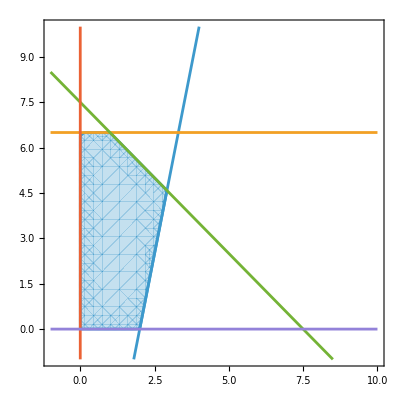

```mathematica
Show[rp,cp]
```

Som ønsket

### (d)

Vi løser problemet med branch and bound algoritmen. I vores nuværende løsning er

z=15.83
x_1=2.92
x_2=4.58

Vi brancher med udgangspunkt i x_2 og laver derfor to nye begrænsninger x_2>=5 og x_2<=4. Lad os først branche med udgangspunkt i den første af de to begrænsninger, altså x_2>=5. Her fås:

Vi brancher igen, med x_1<=2 og x_1>=3, vi starter med x_1<=2

Dermed er denne branch fathomed. Vi undersøger x_1>=3. Her er ingen løsning, da mulighedsområdet forsvinder

Derefter undersøger vi den anden af de første to begrænsninger, altså x_2<=4

Da ser vi at x_2 er heltalig, men det er x_1 ikke. Dermed får vi begrænsningernerne x_1<=2 og x_1>=3. Vi starter med at branche efter x_1<=2

Denne løsning dominerer den vi fandt før, og er nu vores nye bedste bud. Denne branch er fathomed. 
Vi undersøger for x_1>=3

Her forsvinder mulighedsområdet (ligesom før) og dermed bliver den optimale løsning x_1=2 og x_2=0.

### (f)

Vi udfører en iteration af gomorys algoritme. Først løser vi problemet med simplex hvilket giver følgende optimale tableau

Derefter vælger vi en besisrække, som ikke indeholder en slack variabel. Vi vælger den første række, den med x_1. Da får vi følgende ligning som vi derefter runder ned til nærmeste heltallige koefficienter

x_1+0.08 s_1+0.08 s_3=2.92
x_1=2

Hvilket giver begrænsningen x_1<=2. Vi trækker den nedrundede ligning fra den originale

x_1+0 s_1+0 s_2=2
x_1+0.08 s_1+0.08 s_3=2.92
-0.08 s_1-0.08 s_3=-0.92

Vi tilføjer endnu en slackvariabel s_4 og får ligningen

-0.08 s_1-0.08 s_3+s_4=-0.92

Denne tilføjes til tableauet, hvorefter vi finder det nye optimale tableuau

## Opgave 3

### (a)

Eftersom vi har med et maksimeringsproblem, binære varaible og kun en bibetingelse, kan vi se at vi har med et knapsack problem at gøre.

### (b)

Vi løser problemet med en grådighedsalgoritme. Vi ser at de højeste koeefficienter er i denne rækkefølge

1.->x_5
2.->x_4
3.->x_3
4.->x_1
5.->x_2

Vi starter med at inkludere x_5 og derefter x_4 i vores basis. Da får vi at 7+6=13 og vi kan dermed kun inkludere x_2 uden at bruge bibetingelsen. Dermed bliver løsningen x_5=x_4=x_2=1 imens alle andre variable er nul. Her bliver objektfunktionen 24+20+12=56.

### (c)

Vi løser problemet med simplex metoden

Vi ser at vi får en optimal løsning med (x_1,x_2,x_3,x_4,x_5)=(1,1,0,0.29,1). Eftersom alle koefficienter er positive, vores variable er heltal, og objektfunktionen antager værdien 56.71, ved vi at den optimale løsning må have end objektfunktion med en værdi som er mindre end eller lig 56. Vi ser at hvis vi inkludere s_2 i vores basis, vil objektfunktionen falde med netop 0.71 hvilket giver en værdi af objektfunktionen på 56. Hvis vi vælger s_2 som vores pivot søjle, kan vi enten erstatte denne med x_1 eller s_5. Hvis vi vælger x_1 ser vi at vi får:

Hvilket altså må være den optimale løsning. Her er objektfunktionen 56 og vi ser at vi får samme løsning som med grådighedsalgoritmen.

## Opgave 4: real world med heltal (samme som fra u1) og gomorys cut

Vi husker at problemet bliver nedenstående. For at se nærmere på antagelser, så se samme ogpave fra ugeseddel 1

max 120 x_1+200 x_2+260 x_3
u.b.b
x_1+x_2+x_3<=11
30 x_1+15 x_2+45 x_3<=300
40 x_1+80 x_2+120 x_3<=820
x_1,x_2,x_3>=0

Vi løser problemet med simplex

-Graphics-

-Graphics-

Vi ser at ovenstående bliver den optimale løsning.

### (c)

Vi løser problemet med de nye informationer

Vi ser at objektivfunktionen falder fra 2080 til 2040 som er et tab i salg på 40 mio. kr.

### (d)

Vi husker at det optimale tableau bliver

Hvis vi vælger x_1 som variablen vi vil udføre en et “cut” på, har vi følgende ligning

x_1-x_3+2 s_1-0.03 s_3=1.5

Vi runder ned til nærmeste heltal

x_1-x_3+2 s_1-0 s_3=1

Vi trækker den nedrundede ligning fra den ikke-nedrundede ligning

-0.03 s_3=-0.5

Dermed bliver den nye betingelse -0.03 s_3+s_4<=-0.5

## Ugeseddel 5: Transport, Assignment, TSP

## Opgave 1: assignment problem

### Opgave 1: Det klassiske assignment problem

### (a)

Vi opstiller problemet. Det er et minimeringsproblem, da vi gerne vil minimerer omkostninger. Dette ses herunder

Minimer Z=8 x_AA+6 x_AB+5 x_AC+7 x_AD+6 x_BA+5 x_BB+3 x_BC+4 x_BD+7 x_CA+8 x_CB+5 x_CC+6 x_CD+6 x_DA+7 x_DB+5 x_DC+6 x_DD

u.b.b
x_A_A+x_A_B+x_A_C+x_A_D=1.0
x_B_A+x_B_B+x_B_C+x_B_D=1.0
x_C_A+x_C_B+x_C_C+x_C_D=1.0
x_D_A+x_D_B+x_D_C+x_D_D=1.0
x_A_A+x_B_A+x_C_A+x_D_A=1.0
x_A_B+x_B_B+x_C_B+x_D_B=1.0
x_A_C+x_B_C+x_C_C+x_D_C=1.0
x_A_D+x_B_D+x_C_D+x_D_D=1.0

Samt:x_A_A∈{0,1},x_A_B∈{0,1},x_A_C∈{0,1},x_A_D∈{0,1},x_B_A∈{0,1},x_B_B∈{0,1},x_B_C∈{0,1},x_B_D∈{0,1},x_C_A∈{0,1},x_C_B∈{0,1},x_C_C∈{0,1},x_C_D∈{0,1},x_D_A∈{0,1},x_D_B∈{0,1},x_D_C∈{0,1},x_D_D∈{0,1}

Vi løser først problemet ved brug af computeren:

Objektivfunktionens værdi: 21
-Graphics-

Derefter løser vi problemet med, the hungarian algorithm:

### (c)

Dette er et eksempel på traveling salesman problemet.

### (d)

Løsning nummer 2, er ikke mulig, eftersom man i traveling salesman problem ikke kan tage fra by C til by C. 
Løsning nummer 1 er mulig, da man tager fra A →B→C→D→A.

## Opgave 2: Transportation problem

### (a)

Vi ser at efterspørgslen er 3+3+2+2=10 og at udbud er 5+2+3=10, og dermed er transportalgoritmens antagelser opfyldt.

### (b)

Vi starter med at benytte northwest corner metoden.

Vi ser at objektivfunktionens værdi her bliver

```mathematica
3*3+2*7+4+3+8+2*5
```

48

Derefter finder vi en mulig løsning med vogels approksimation

Og til sidst med minimum column rule

Det er helt klar vogels approksimation som er bedst, da den resulterer i den laveste værdi af objektfunktionen.

```mathematica
2^5-5-1
```

26

Vi løser problemet med transport algoritmen. 
Vi starter med startgættet fra vogels approksimation

| D_1 | D_2 | D_3 | D_4 | B
A | 3 | 0 | 0 | 2 | 5
B |   |   |  2 |   | 2
C |   | 3 |   |   | 3
E | 3 | 3 | 2 | 2 | 32 og 3 | 7 | 6 | 4
2 | 4 | 3 | 2
4 | 3 | 8 | 5

Vi opstiller nu ligningerne u_i+v_j=c_(i j)∀i,j hvor der er basisvariable. Vi får ligningerne

u_1+v_1=3
u_1+v_2=7
u_1+v_3=6
u_1+v_4=4
u_2+v_3=3
u_3+v_2=3

Da systemet er overbestemt (antal variable > antal ligninger) sætter vi u_1=0 og løser systemet

```mathematica
Solve[{
u1+v1==3,
u1+v2==7,
u1+v3==6,
u1+v4==4,
u2+v3==3,
u3+v2==3,
u1==0
}]
```

{{u1→0,u2→-3,u3→-4,v1→3,v2→7,v3→6,v4→4}}

Vi ser at

u_1=0
u_2=-3
u_3=-4
v_1=3
v_2=7
v_3=6
v_4=4

Derefter beregner vi de reducerede omkostninger (c̄)_(p q)=c_(p q)-u_p-v_q for alle variable som ikke optræder i basen. 
Vi har ikke basisvariable x_21,x_22,x_24,x_31,x_33,x_34. Da bliver

(c̄)_21=2-(-3)-(3)=2
(c̄)_22=4-(-3)-7=0
(c̄)_24=2-(-3)-4=1
(c̄)_31=4-(-4)-3=5
(c̄)_33=8-(-4)-6=6
(c̄)_34=5-(-4)-4=5

Indsat i vores tableau giver de nedenstående, hvor felter, som ikke er markedet med fed, er de reducerede omkostninger (slackvariable i det duale program)

| D_1 | D_2 | D_3 | D_4 | B
A | 3 | 0 | 0 | 2 | 5
B |  2 | 0  |  2 | 1  | 2
C | 5  | 3 |  6 | 5  | 3
E | 3 | 3 | 2 | 2 | 32

Da alle slackvariable er positive, er det den optimale løsning, som vi fandt med udgangspunkt i vogels approksimation!

## Opgave 3: Assignment problem

Der er tale om et assignment problem, da hver kunde skal have en bil, og hver bil skal afsættes til en kunde. Vi løser problemet med computeren (løst i julia):

Som ønsket. Vi ser at

bil 1->Kaj
bil 2->Martin
bil 3->Henning
bil 4->Mike
bil 5->Jens

Hvilket betyder at bil 1 går til Kaj osv.

## Opgave 4: Transportation problem

### (a) og (b):

Der er tale om et transportation problem, da hver varetype skal indgå netop en gang i produktionsrækkefølgen. 
Vi løser problemet i Julia:

Som ønsket

## Opgave 5

### (a)

Jeg benytter forkortelser for navnene. Først laves en oversigt over de forskellige omkostninger på routen

ca->wh=16
wh->ta=10
ta->kr=8
kr->cr=8.5
cr->ca=13.5

Hvilket giver det samlede omkostnigner 16+10+8+9.5+13.5=56.

### (b)

Vi løser problemet

Da passer også godt med mit resultat

### (d)

Før brugte han

```mathematica
56*5
```

280

miinutter og nu bruger han

```mathematica
48*5
```

240

Minutter, så kan sparer 40 minutter!!!

## Ugeseddel 6: MST

## Opgave 1: minimum spanning tree

### (a)

Dette er et eksempel på minimum spanning tree problemet, da alle noder skal sammensættes med edges til den laveste mulige omkostning.

Vi løser problemet med kruskals algoritme. Vi opstiller alle edges fra mindst til højest og benytter algoritmen

Node 1 | Node 2 | Vægt | Inkluderet
B | C | 1 | ja
A | B | 2 | ja
E | H | 2 | ja
D | C | 3 | ja
C | E | 3 | ja
F | H | 3 | ja
A | C | 4 | nej
B | E | 4 | nej
C | F | 4 | nej
G | H | 4 | ja
A | D | 5 | nej
A | E | 5 | nej
C | F | 5 | nej
G | F | 5 | nej
D | G | 6 | nej
D | H | 7 | nej

### (b)

Her ses resultatet

```mathematica
2+1+3+3+4+2+3
```

18

Det er et andet, ligeså legitimt resultat.

## Opgave 2: shortest path

Her er djikstars algoritme benyttet

Den korteste vej fra r til s bliver altså (opstilles fra højre til venstre da det er nemmere): s < c < d < a < b < q < r.

Vi dobbelttjekker med julia:

Og der fås samme løsning.

## Opgave 3: Maximum flow (algoritme ikke lært)

### (d)

Vi har lavet beslutningsvariablene som outflow fra københavn.

Betingelserne er flow betingelserne, altså at der ikke er mere flow end der må være, og at samlet ind flow - samlet udflow =0. Her ses de eksplicit

Hvor x_by1_by2 er flow fra den by1 til by2.

Vi får følgende løsning

## Opgave 4: minimum spanning tree

Vi

Node | Node | Vægt | Inkluderet
3 | 6 | 1 | ja
2 | 3 | 2 | ja
2 | 5 | 3 | ja
5 | 6 | 3 | nej
1 | 2 | 4 | ja
6 | 9 | 4 | ja
5 | 9 | 4 | nej
3 | 7 | 6 | ja
5 | 8 | 6 | ja
1 | 6 | 7 | nej
7 | 9 | 7 | nej
4 | 8 | 8 | ja
8 | 9 | 8 | nej
1 | 3 | 9 | nej
1 | 4 | 11 | nej
4 | 7 | 12 | nej

Her ses mit resulatet

Her ses resultatet fra julia:

Selvom træerne ikke er helt ens, giver de samme objektivværdi, og alle tre resultater antages at være løsninger.

## Opgave 5: Maximum flow (ikke lært algoritme)

Vi løser problemet i julia:

## Opgave 6: maksimum flow (ikke lært algoritme) (ikke lavet opgave)

## Ugeseddel 8: Kø-teori

## Opgave 1

### a.

For at alle kunderne skal kunne blive betjent, skal have en utilisation, som er under 1 (100%).
For at beregne denne skal vi kende arrival rate og processing rate. Vi ved at det forventes at der kommer 3 kunder hvert minut, svarende til at der kommer 3*60=180 kunder pr. time. Dermed bliver arrival rate pr. time

λ=1/180=0.00555556

Svarende til at der kommer en kunde hvert 0.0055556 time. En assistent kan i gennemsnit betjene 75 kunder i timen. Processing rate beregnes nu i pr. time endheder

μ=1/75=0.0133333

Vi vil gerne have at utilisation <1, og vi skal vælge N således at dette bliver tilfældet. Dermed kan vi skrive at

ρ=λ/(N*μ)<1

(1/180)/(N*1/75)<1
5/(12N)<1
5<12N
5/12<N

Dermed skal man hyre mindst en medarbejder, for at utilisation rate er under 1.